```mathematica
allNull4Sorted=Sort[allNull4,CompareSymbols[allGraphs4[#1,"colofourrealnull"],allGraphs4[#2,"colofourrealnull"]]&]
```

{0,2,18,6,486,162,54,26,488,666,546,168,218,72,728}

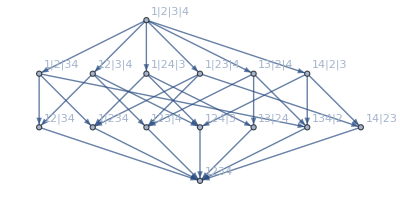

```mathematica
fullMob =With[{g= MobiusGraph4[K4Key,allGraphs4]},Graph[Table[allGraphs4[k,"colofourrealnull"],{k,allNull4Sorted}],
Sort[EdgeList[g],CompareSymbols[#1[[1]],#2[[2]]]&],VertexLabels->Table[allGraphs4[k,"colofourrealnull"]->SymbolToLabel[allGraphs4[k,"colofourrealnull"]],{k,allNull4Sorted}],GraphLayout->"LayeredDigraphEmbedding"]]
```

```mathematica
headers={Table[SymbolToLabel[allGraphs4[k,"colofourrealnull"]],{k,allNull4Sorted}], Table[Rotate[SymbolToLabel[allGraphs4[k,"colofourrealnull"]],Pi/2],{k,allNull4Sorted}]}
```

{{1|2|3|4,1|2|34,1|23|4,1|24|3,12|3|4,13|2|4,14|2|3,1|234,12|34,123|4,124|3,13|24,134|2,14|23,1234},{1|2|3|4,1|2|34,1|23|4,1|24|3,12|3|4,13|2|4,14|2|3,1|234,12|34,123|4,124|3,13|24,134|2,14|23,1234}}

```mathematica
MatrixForm[AdjacencyMatrix[fullMob],TableHeadings->headers]
```

( | 1|2|3|4 | 1|2|34 | 1|23|4 | 1|24|3 | 12|3|4 | 13|2|4 | 14|2|3 | 1|234 | 12|34 | 123|4 | 124|3 | 13|24 | 134|2 | 14|23 | 1234
1|2|3|4 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1|2|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
1|23|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1|24|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
12|3|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
13|2|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0
14|2|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
1|234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
12|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
123|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
124|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
13|24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
134|2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
14|23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[MatrixPower[AdjacencyMatrix[fullMob]+IdentityMatrix[15],2],TableHeadings->headers]
```

( | 1|2|3|4 | 1|2|34 | 1|23|4 | 1|24|3 | 12|3|4 | 13|2|4 | 14|2|3 | 1|234 | 12|34 | 123|4 | 124|3 | 13|24 | 134|2 | 14|23 | 1234
1|2|3|4 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 0
1|2|34 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 3
1|23|4 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 3
1|24|3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 3
12|3|4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 3
13|2|4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 3
14|2|3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 3
1|234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2
12|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2
123|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2
124|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2
13|24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2
134|2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2
14|23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
1234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[MobiusMatrix[allGraphs4]//Inverse,TableHeadings->headers]
```

( | 1|2|3|4 | 1|2|34 | 1|23|4 | 1|24|3 | 12|3|4 | 13|2|4 | 14|2|3 | 1|234 | 12|34 | 123|4 | 124|3 | 13|24 | 134|2 | 14|23 | 1234
1|2|3|4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1|2|34 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1|23|4 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1
1|24|3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
12|3|4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
13|2|4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
14|2|3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
1|234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
12|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
123|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
124|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
13|24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
134|2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
14|23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[zet]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Map[Map[If[#>0,1,0]&,#]&,MatrixPower[AdjacencyMatrix[fullMob]+IdentityMatrix[15],2]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{0,1,0,0,0,0,0,1,1,0,0,0,1,0,1},{0,0,1,0,0,0,0,1,0,1,0,0,0,1,1},{0,0,0,1,0,0,0,1,0,0,1,1,0,0,1},{0,0,0,0,1,0,0,0,1,1,1,0,0,0,1},{0,0,0,0,0,1,0,0,0,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,0,1,0,1,1,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Map[Map[If[#>0,1,0]&,#]&,MatrixPower[AdjacencyMatrix[fullMob]+IdentityMatrix[15],2]]==Inverse[MobiusMatrix[allGraphs4]]
```

False

```mathematica
tt=Map[Map[If[#>0,1,0]&,#]&,MatrixPower[AdjacencyMatrix[fullMob]+IdentityMatrix[15],3]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,1,1,0,0,0,1,0,1},{0,0,1,0,0,0,0,1,0,1,0,0,0,1,1},{0,0,0,1,0,0,0,1,0,0,1,1,0,0,1},{0,0,0,0,1,0,0,0,1,1,1,0,0,0,1},{0,0,0,0,0,1,0,0,0,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,0,1,0,1,1,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
tt==Inverse[MobiusMatrix[allGraphs4]]
```

True